```mathematica
delta=2;
a=1;
b=11;
```

```mathematica
partition=Partition[Table[i,{i,a,b,delta}],2,1];
```

```mathematica
partition⟦1;;3⟧
```

{{1,3},{3,5},{5,7}}

```mathematica
varSeries={1,2,3,3.2,3.2,3.5,3.6,4,4.1,4.5,5.4,6.1,7.1,7.3,7.4,8.3,9,10,10.1};
counts=ConstantArray[0,Length@partition];
```

```mathematica
Do[Do[If[partition⟦j,1⟧< varSeries⟦i⟧&&varSeries⟦i⟧≤ partition⟦j,2⟧,counts⟦j⟧++],{j,1,Length@partition}],{i,1,Length@varSeries}]
```

```mathematica
counts
```

{2,7,2,5,2}

```mathematica
frequency=counts/delta;
```

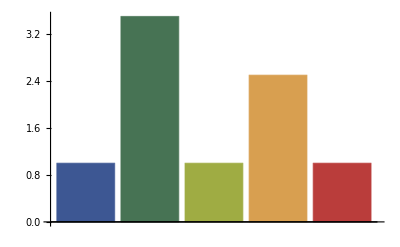

```mathematica
BarChart[frequency,ChartStyle->"DarkRainbow"]
```

#### Теорема Колмогорова

```mathematica
Table[∑_(j=-∞)^∞ (-1)^j ⅇ^(-2 j^2 x^2),{x,0.1,3,0.1}]//N
```

{0.,5.04985×10^-13,9.3058×10^-6,0.00280767,0.0360548,0.135717,0.288765,0.455858,0.607269,0.73,0.822282,0.88775,0.931908,0.960318,0.977782,0.988048,0.993823,0.996932,0.998536,0.999329,0.999705,0.999875,0.999949,0.99998,0.999993,0.999997,0.999999,1.,1.,1.}

```mathematica
2/√100//N
```

0.2

```mathematica
√(400*500/900)//N
```

14.9071

```mathematica
0.5/14.9
```

0.033557